```mathematica
allCritVars=Sort[DeleteDuplicates[ListofVars[allCrit]],CompareSymbols]
```

{v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v124x35,v134x25,v135x24,v13x245,v14x235}

```mathematica
BaseCoeff3[formula_,base_]:=Table[Coefficient[formula,var],{var,allCritVars}]
```

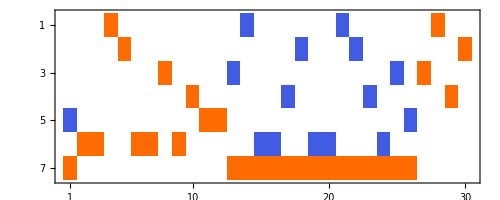

```mathematica
MatrixPlot[Map[BaseCoeff3[Total[ListofVars[#]],"C"]&,Select[ExpressionToList[allCrit],Length[#]==15&]]//LatticeReduce,TableHeadings
```

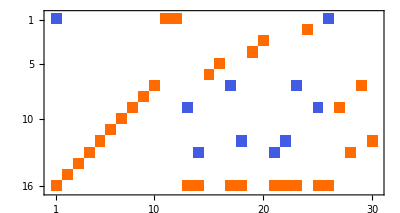

```mathematica
MatrixPlot[Map[BaseCoeff3[Total[ListofVars[#]],"C"]&,ExpressionToList[allCrit]]//LatticeReduce//Sort]
```

```mathematica
MatrixRank[Map[BaseCoeff3[Total[ListofVars[#]],"C"]&,ExpressionToList[allCrit]]//LatticeReduce//Sort]
```

16

```mathematica
tri
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
quad=Table[allGraphs5[k,"colofour"],{k,quads}]
```

{v13x2x4x5,v1x24x3x5,v1x2x35x4,v14x2x3x5,v1x25x3x4}

```mathematica
repquad=Table[allGraphs5[k,"colofour"]->Style[allGraphs5[k,"colofour"],Green],{k,quads}]
```

{v13x2x4x5→v13x2x4x5,v1x24x3x5→v1x24x3x5,v1x2x35x4→v1x2x35x4,v14x2x3x5→v14x2x3x5,v1x25x3x4→v1x25x3x4}

```mathematica
reptri=Table[allGraphs5[k,"colofour"]->Style[allGraphs5[k,"colofour"],Red],{k,alfa1s}]
```

{v13x24x5→v13x24x5,v14x25x3→v14x25x3,v1x24x35→v1x24x35,v13x25x4→v13x25x4,v14x2x35→v14x2x35}

```mathematica
Map[ListofVars,ExpressionToList[allCrit]]/.reptri/.repquad
```

{{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x35,v12x3x4x5,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x35,v12x3x4x5,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x3x4,v1x2x34x5,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x3x4,v1x2x34x5},{v124x3x5,v12x35x4,v134x25,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x24,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x24x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x25x4,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x35,v1x25x34,v1x25x3x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4,v1x2x3x45},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x24x5,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x25x4,v13x2x45,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x25x3,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x35,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x24x3,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x25x3,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x2x35x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x35,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4}}

```mathematica
Map[With[{v=ListofVars[#]},{Length[Intersection[v,tri]],Length[Intersection[v,quad]]}]&,ExpressionToList[allCrit]]//Sort
```

{{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0}}

Part::partd: Part specification v124x35⟦1⟧ is longer than depth of object.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

Part::partd: Part specification v124x35⟦1⟧ is longer than depth of object.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

Part::partd: Part specification v124x35⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

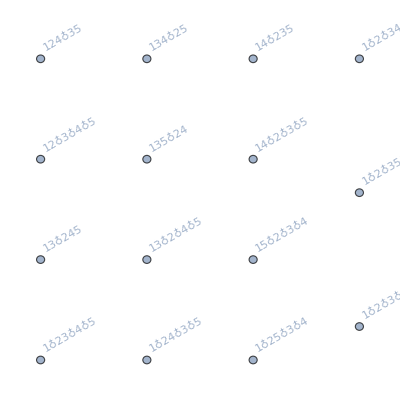
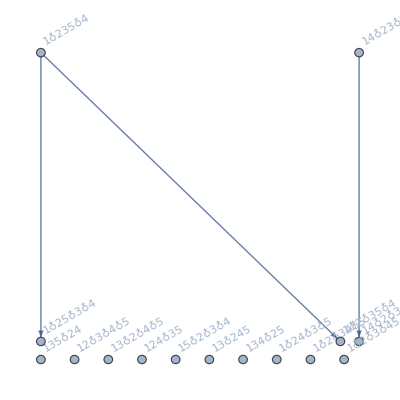
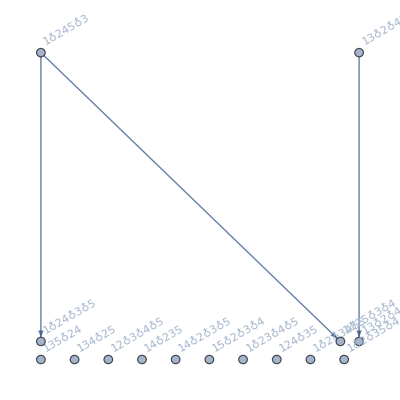
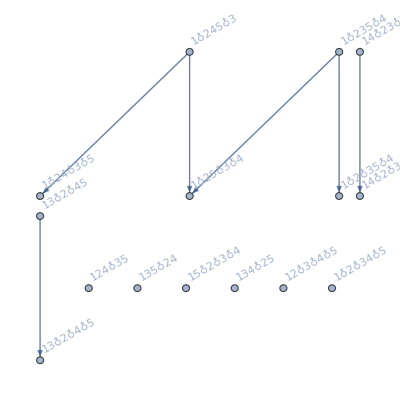
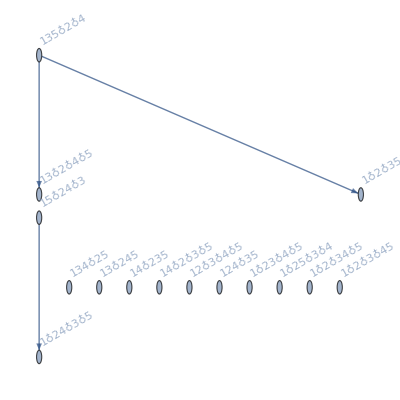
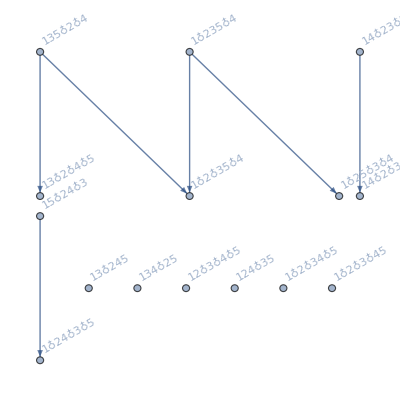
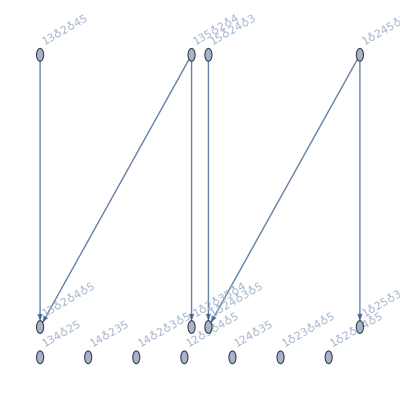
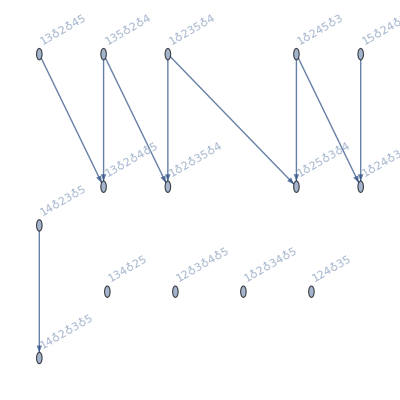

```mathematica
Map[FormulaGraphReverse2[Total[#]]&,Select[Map[ListofVars,ExpressionToList[allCrit]],Intersection[#,tri]=={}&]]
```

```mathematica
BaseCoeff4[formula_,base_]:=Table[Coefficient[formula,var],{var,SetDifference[allCritVars,tri]}]
```

```mathematica
CoeffExpand[vect_]:=vect.Table[var,{var,SetDifference[allCritVars,tri]}]
```

Part::partd: Part specification v13x245⟦1⟧ is longer than depth of object.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

Part::partd: Part specification v13x245⟦1⟧ is longer than depth of object.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

Part::partd: Part specification v13x245⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

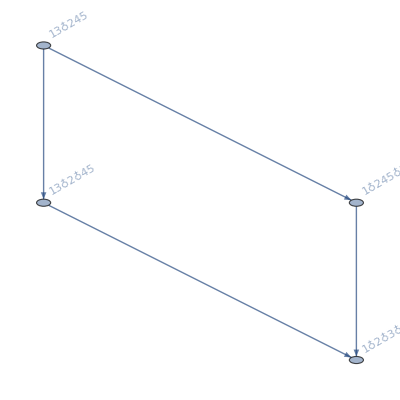
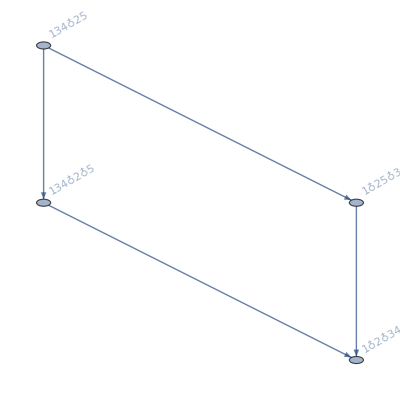
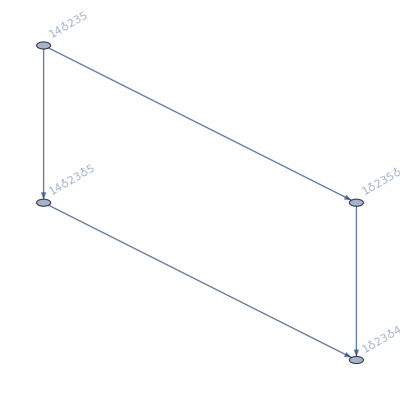
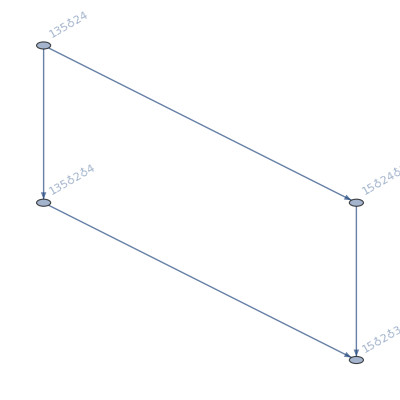
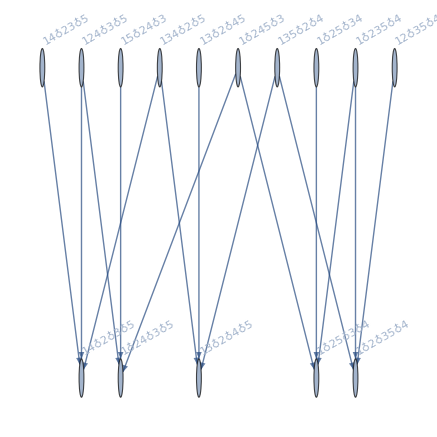
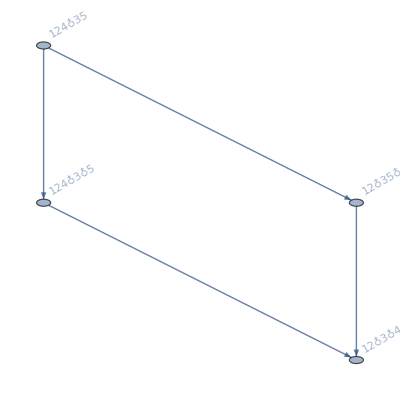

```mathematica
Map[FormulaGraphReverse2[CoeffExpand[#]]&,Map[BaseCoeff4[Total[ListofVars[#]],"C"]&,Select[Map[ListofVars,ExpressionToList[allCrit]],Intersection[#,tri]=={}&]]//LatticeReduce//Sort]
```

```mathematica
Clear[RepAtLeast2];RepAtLeast2[base_]:=RepAtLeast2[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->Labeled[Framed[Style[allGraphs5[key,"atleast"],Red,Bold,12]],allGraphs5[key,Bases[base,"Colofour"]]],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
RepAtLeast2["C"]
```

{v1x2x3x4x5→0v1x2x3x4x5,v12x3x4x5→0v12x3x4x5,v13x2x4x5→0v13x2x4x5,v14x2x3x5→0v14x2x3x5,v15x2x3x4→0v15x2x3x4,v1x23x4x5→0v1x23x4x5,v1x24x3x5→0v1x24x3x5,v1x25x3x4→0v1x25x3x4,v1x2x34x5→0v1x2x34x5,v1x2x35x4→0v1x2x35x4,v1x2x3x45→0v1x2x3x45,v123x4x5→1v123x4x5,v124x3x5→0v124x3x5,v125x3x4→1v125x3x4,v12x34x5→1v12x34x5,v12x35x4→0v12x35x4,v12x3x45→1v12x3x45,v134x2x5→0v134x2x5,v135x2x4→0v135x2x4,v13x24x5→0v13x24x5,v13x25x4→0v13x25x4,v13x2x45→0v13x2x45,v145x2x3→1v145x2x3,v14x23x5→0v14x23x5,v14x25x3→0v14x25x3,v14x2x35→0v14x2x35,v15x23x4→1v15x23x4,v15x24x3→0v15x24x3,v15x2x34→1v15x2x34,v1x234x5→1v1x234x5,v1x235x4→0v1x235x4,v1x23x45→1v1x23x45,v1x245x3→0v1x245x3,v1x24x35→0v1x24x35,v1x25x34→0v1x25x34,v1x2x345→1v1x2x345,v1234x5→1v1234x5,v1235x4→1v1235x4,v123x45→1v123x45,v1245x3→1v1245x3,v124x35→0v124x35,v125x34→1v125x34,v12x345→1v12x345,v1345x2→1v1345x2,v134x25→0v134x25,v135x24→0v135x24,v13x245→0v13x245,v145x23→1v145x23,v14x235→0v14x235,v15x234→1v15x234,v1x2345→1v1x2345,v12345→1v12345}

```mathematica
v1x2x3x4x5+v1245x3/.RepAtLeast2["C"]
```

0v1x2x3x4x5+1v1245x3

```mathematica
Map[CoeffExpand[#]&,Map[BaseCoeff4[Total[ListofVars[#]],"C"]&,Select[Map[ListofVars,ExpressionToList[allCrit]],Intersection[#,tri]=={}&]]//LatticeReduce//Sort]/.RepAtLeast2["C"]
```

{0v13x245-0v13x2x45-0v1x245x3+0v1x2x3x45,0v134x25-0v134x2x5-0v1x25x34+0v1x2x34x5,0v14x235-0v14x23x5-0v1x235x4+0v1x23x4x5,0v135x24-0v135x2x4-0v15x24x3+0v15x2x3x4,0v124x3x5+0v12x35x4+0v134x2x5+0v135x2x4+0v13x2x45+0v13x2x4x5+0v14x23x5+0v14x2x3x5+0v15x24x3+0v1x235x4+0v1x245x3+0v1x24x3x5+0v1x25x34+0v1x25x3x4+0v1x2x35x4,0v124x35-0v124x3x5-0v12x35x4+0v12x3x4x5}

```mathematica
Map[(CoeffExpand[#])&,Map[BaseCoeff4[Total[ListofVars[#]],"C"]&,Select[Map[ListofVars,ExpressionToList[allCrit]],Intersection[#,tri]=={}&]]//LatticeReduce//Sort]
```

{v13x245-v13x2x45-v1x245x3+v1x2x3x45,v134x25-v134x2x5-v1x25x34+v1x2x34x5,v14x235-v14x23x5-v1x235x4+v1x23x4x5,v135x24-v135x2x4-v15x24x3+v15x2x3x4,v124x3x5+v12x35x4+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v14x23x5+v14x2x3x5+v15x24x3+v1x235x4+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x35x4,v124x35-v124x3x5-v12x35x4+v12x3x4x5}

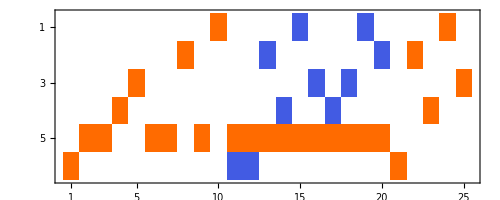

```mathematica
MatrixPlot[Map[BaseCoeff4[Total[ListofVars[#]],"C"]&,Select[Map[ListofVars,ExpressionToList[allCrit]],Intersection[#,tri]=={}&]]//LatticeReduce//Sort]
```

```mathematica
Length[ExpressionToList[allCrit]]
```

544

```mathematica
FactorInteger[544]
```

{{2,5},{17,1}}

## TRy to do one crit

```mathematica
ListofVars[allCrit[[1]]]/.RepKey["C"]
```

{51478,49207,38308,36898,36194,36166,36112,31984,31738,31714,30253,29767,29608,29533,29525}

```mathematica
Table[ShowGraph5Least[k],{k,ListofVars[allCrit[[1]]]/.RepKey["C"]}]
```

{-Graphics-514781,-Graphics-492071,-Graphics-383081,-Graphics-368981,-Graphics-361941,-Graphics-361661,-Graphics-361121,-Graphics-319841,-Graphics-317381,-Graphics-317141,-Graphics-302531,-Graphics-297671,-Graphics-296081,-Graphics-295331,-Graphics-295251}

```mathematica
Table[allGraphs5[k,"comp"]=Greater;allGraphs5[k,"compwhy"]=ToString[allCrit[[1]]];
allGraphs5[k,"atleast"]=1;allGraphs5[k,"atleastwhy"]=ToString[allCrit[[1]]],{k,ListofVars[allCrit[[1]]]/.RepKey["C"]}]
```

{v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0,v124x35 > 0 && v12x3x4x5 > 0 && v134x25 > 0 && v135x24 > 0 && v13x245 > 0 && v13x24x5 > 0 && v13x25x4 > 0 && v14x235 > 0 && v14x25x3 > 0 && v14x2x35 > 0 && v15x2x3x4 > 0 && v1x23x4x5 > 0 && v1x24x35 > 0 && v1x2x34x5 > 0 && v1x2x3x45 > 0}

```mathematica
PropagateComp[]
```

The relation holds 29520(GreaterEqual)== 29521(GreaterEqual) + 29525 (Greater) (greater propagated from right)

The relation holds 29523(GreaterEqual)== 29524(Equal) + 29525 (Greater) (greater propagated from right)

The relation holds 29514(GreaterEqual)== 29523(Greater) + 29533 (Greater) (greater propagated from left)

The relation holds 29515(GreaterEqual)== 29524(Equal) + 29533 (Greater) (greater propagated from right)

The relation holds 29512(GreaterEqual)== 29521(GreaterEqual) + 29533 (Greater) (greater propagated from right)

The relation holds 29493(GreaterEqual)== 29520(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 29496(GreaterEqual)== 29523(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 29574(GreaterEqual)== 29577(GreaterEqual) + 29608 (Greater) (greater propagated from right)

The relation holds 29602(GreaterEqual)== 29605(GreaterEqual) + 29608 (Greater) (greater propagated from right)

The relation holds 29439(GreaterEqual)== 29520(Greater) + 29602 (Greater) (greater propagated from left)

The relation holds 29442(GreaterEqual)== 29523(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29446(GreaterEqual)== 29527(GreaterEqual) + 29608 (Greater) (greater propagated from right)

The relation holds 29440(GreaterEqual)== 29521(GreaterEqual) + 29602 (Greater) (greater propagated from right)

The relation holds 29433(GreaterEqual)== 29514(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29434(GreaterEqual)== 29515(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29431(GreaterEqual)== 29512(Greater) + 29602 (Greater) (greater propagated from left)

The relation holds 29281(GreaterEqual)== 29524(Equal) + 29767 (Greater) (greater propagated from right)

The relation holds 29278(GreaterEqual)== 29521(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29272(GreaterEqual)== 29515(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29269(GreaterEqual)== 29512(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29254(GreaterEqual)== 29497(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29200(GreaterEqual)== 29443(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29197(GreaterEqual)== 29440(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29173(GreaterEqual)== 29416(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29176(GreaterEqual)== 29446(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 28791(GreaterEqual)== 29520(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28794(GreaterEqual)== 29523(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28795(GreaterEqual)== 29524(Equal) + 30253 (Greater) (greater propagated from right)

The relation holds 28792(GreaterEqual)== 29521(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28764(GreaterEqual)== 29493(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28767(GreaterEqual)== 29496(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28768(GreaterEqual)== 29497(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28765(GreaterEqual)== 29494(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28845(GreaterEqual)== 29574(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The relation holds 28873(GreaterEqual)== 29602(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The relation holds 31708(GreaterEqual)== 31711(GreaterEqual) + 31714 (Greater) (greater propagated from right)

The relation holds 31684(GreaterEqual)== 31711(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 31465(GreaterEqual)== 31708(Greater) + 31954 (GreaterEqual) (greater propagated from left)

The relation holds 31492(GreaterEqual)== 31738(Greater) + 31984 (Greater) (greater propagated from left)

The relation holds 31441(GreaterEqual)== 31684(Greater) + 31954 (GreaterEqual) (greater propagated from left)

The relation holds 31444(GreaterEqual)== 31714(Greater) + 31984 (Greater) (greater propagated from left)

The relation holds 27333(GreaterEqual)== 29520(Greater) + 31708 (Greater) (greater propagated from left)

The relation holds 27336(GreaterEqual)== 29523(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27340(GreaterEqual)== 29527(GreaterEqual) + 31714 (Greater) (greater propagated from right)

The relation holds 27334(GreaterEqual)== 29521(GreaterEqual) + 31708 (Greater) (greater propagated from right)

The relation holds 27327(GreaterEqual)== 29514(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27328(GreaterEqual)== 29515(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27325(GreaterEqual)== 29512(Greater) + 31708 (Greater) (greater propagated from left)

The relation holds 27355(GreaterEqual)== 29542(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 27364(GreaterEqual)== 29551(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 27309(GreaterEqual)== 29496(Greater) + 31684 (Greater) (greater propagated from left)

The relation holds 27310(GreaterEqual)== 29497(GreaterEqual) + 31684 (Greater) (greater propagated from right)

The relation holds 27255(GreaterEqual)== 29442(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27246(GreaterEqual)== 29433(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27247(GreaterEqual)== 29434(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27273(GreaterEqual)== 29460(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 27282(GreaterEqual)== 29469(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 26608(GreaterEqual)== 28795(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 26605(GreaterEqual)== 28792(Greater) + 31708 (Greater) (greater propagated from left)

The relation holds 26581(GreaterEqual)== 28768(Greater) + 31684 (Greater) (greater propagated from left)

The relation holds 36057(GreaterEqual)== 36084(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 36058(GreaterEqual)== 36085(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 36138(GreaterEqual)== 36166(Greater) + 36194 (Greater) (greater propagated from left)

The relation holds 36003(GreaterEqual)== 36084(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 36004(GreaterEqual)== 36085(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 36030(GreaterEqual)== 36112(Greater) + 36194 (Greater) (greater propagated from left)

The relation holds 35325(GreaterEqual)== 36057(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 35326(GreaterEqual)== 36058(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 35406(GreaterEqual)== 36138(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 35434(GreaterEqual)== 36166(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 33916(GreaterEqual)== 36112(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 33807(GreaterEqual)== 36003(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 33808(GreaterEqual)== 36004(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 33834(GreaterEqual)== 36030(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 22954(GreaterEqual)== 29515(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22951(GreaterEqual)== 29512(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22981(GreaterEqual)== 29542(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22990(GreaterEqual)== 29551(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22936(GreaterEqual)== 29497(GreaterEqual) + 36058 (Greater) (greater propagated from right)

The relation holds 23044(GreaterEqual)== 29605(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 22882(GreaterEqual)== 29443(GreaterEqual) + 36004 (Greater) (greater propagated from right)

The relation holds 22873(GreaterEqual)== 29434(Greater) + 36004 (Greater) (greater propagated from left)

The relation holds 22720(GreaterEqual)== 29281(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22717(GreaterEqual)== 29278(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22711(GreaterEqual)== 29272(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22708(GreaterEqual)== 29269(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22735(GreaterEqual)== 29296(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22744(GreaterEqual)== 29305(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22693(GreaterEqual)== 29254(Greater) + 36058 (Greater) (greater propagated from left)

The relation holds 22639(GreaterEqual)== 29200(Greater) + 36004 (Greater) (greater propagated from left)

The relation holds 22234(GreaterEqual)== 28795(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22207(GreaterEqual)== 28768(Greater) + 36058 (Greater) (greater propagated from left)

The relation holds 22315(GreaterEqual)== 28876(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 22318(GreaterEqual)== 29608(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 25138(GreaterEqual)== 31708(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 25168(GreaterEqual)== 31738(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 24895(GreaterEqual)== 31465(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 24922(GreaterEqual)== 31492(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 20047(GreaterEqual)== 26608(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 20050(GreaterEqual)== 27340(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 9841(GreaterEqual)== 29524(Equal) + 49207 (Greater) (greater propagated from right)

The relation holds 9814(GreaterEqual)== 29497(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9760(GreaterEqual)== 29443(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9763(GreaterEqual)== 29446(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 9733(GreaterEqual)== 29416(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9598(GreaterEqual)== 29281(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9571(GreaterEqual)== 29254(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9517(GreaterEqual)== 29200(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9490(GreaterEqual)== 29173(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9493(GreaterEqual)== 29176(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 9112(GreaterEqual)== 28795(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 11950(GreaterEqual)== 31714(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 11920(GreaterEqual)== 31684(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11677(GreaterEqual)== 31441(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11680(GreaterEqual)== 31444(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 7654(GreaterEqual)== 27337(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 7657(GreaterEqual)== 27340(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 7627(GreaterEqual)== 27310(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 7738(GreaterEqual)== 29608(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 6925(GreaterEqual)== 26608(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 3280(GreaterEqual)== 22963(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 3253(GreaterEqual)== 22936(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 3199(GreaterEqual)== 22882(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 2551(GreaterEqual)== 22234(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 1093(GreaterEqual)== 20776(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 1174(GreaterEqual)== 23044(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 364(GreaterEqual)== 20047(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 367(GreaterEqual)== 20050(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 445(GreaterEqual)== 22315(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 448(GreaterEqual)== 22318(Greater) + 51478 (Greater) (greater propagated from left)

130

```mathematica
PropagateComp[]
```

0

```mathematica
PropagateAtLeast2[]
```

Propagate from relation {29524, 29525} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 29533} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 29767} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 30253} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 49207} with values {0, 1} and comp {Equal, Greater} (from right)

{5,{}}

```mathematica
PropagateAtLeast2[]
```

{0,{}}

```mathematica
allCrit2=Map[Sort,BooleanMinimize[Reduce[
With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
]]]
```